# Mapping of indoor environments with the Wolfram language and Raspberry Pi

Name: Isaac Ayalaa

Instructor: Ian Johnson

## Homework Solution

### Elevator Pitch

Do you like pie?
What if I told you that pie can make your life easier?

PAI, stands for Personal Artificial Intelligence. It is a product in development, that can aid you in your daily activities.
Unlike other services that limit you to a set of commands in an ordered structure, PAI learns from you and adapts to your needs.

By interacting with it, it improves itself. If you ever need it to do something that it has never done, a demonstration or two of how to do it will be enough for it to learn.

Imagine that you need to submit a report of very specific data, by using Wolfram technologies, PAI is capable of analyzing the things that you ask it to and then generate by itself the paperwork.

By syncing it with your IoT devices, it can do even more. 

Did you forget to turn off the stove? Just ask PAI to do it.
Are you hungry? PAI will offer to call a restaurant for you.
Do you need medical attention? By analyzing data from your wearable devices, PAI will stay alert and call an ambulance immediately.

## Project Description

### Introduction to Simultaneous Localization and Mapping (SLAM)

SLAM considers the action of a robot estimating its position at the same time that it determines the position of objects that it encounters in its path. Because no data is provided about the environment, robots must use sensors to obtain information about its surroundings. 
Several techniques are used to process the information, which can then be used to alter the robots course or to generate visualizations of the results. Such techniques include the use of graph methods to store information, implementation of Kalman filters and Markov chains to compare predictions of the rot’s location and its actual position.

### Proposal

To develop a solution to the SLAM problem with Mathematica, consisting of the following elements :

Algorithm to obtain and store information

Simulations to test the algorithm

Physical implementation

The objective is to generate a 2D map of a robot’s environment through the Wolfram language. A robot is built with the purpose of obtaining data, and feeding it to a Raspberry Pi for processing.
The generation of a map considers the detection of basic geometrical features of objects, with t he possibility of distinguishing obstacles from the room’s delimitation (walls).

#### Algorithm

A cost-effective solution was developed for the Wolfram Science Summer School. The program operates based on digital signals that are read by a Raspberry Pi, which acts as the Main Control Unit for the robot. Movement is possible in four directions: Forward, Back, Right and Left, and collision detection is implemented as part of the algorithm to determine any change in direction.

A Wolfram Data Drop bin is used to store information related to the robot’s path, consisting of: a time object, robot position, sensor readings, collision locations and a list of all locations visited by the robot.

One can observe a simplified version of how the robot operates in figure 1.

```mathematica
Import["https://docs.google.com/drawings/d/1KbLprC-P1dsqzqODmBAHIIJ_D5AMz2gINF2Ngm53XuY/pub?w=915&h=765"]
```

-Graphics-

## Code

### Robot

```mathematica
updateSensors[pins_List]:=Module[{temporary,sensorVector},temporary=DeviceRead["GPIO",pins];sensorVector=Table[temporary[pins[[i]]],{i,Length[pins]}]]
```

```mathematica
getTimeDifference[tNow_,tBefore_]:=Module[{},Round[QuantityMagnitude[UnitConvert[tNow-tBefore,"Seconds"]]]]
```

```mathematica
updatePosition[currentTime_,statusOld_List,speed_List]:=Module[{newPosition,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
newPosition=Piecewise[{{Round[statusOld[[2]]+{0,Δt}*speed], statusOld[[3]]=="Forward"}, {Round[statusOld[[2]]-{0,Δt}*speed], statusOld[[3]]=="Back"}, {Round[statusOld[[2]]-{Δt,0}*speed], statusOld[[3]]=="Left"}, {Round[statusOld[[2]]+{Δt,0}*speed], statusOld[[3]]=="Right"}, {statusOld[[2]], statusOld[[3]]=="Stop"}}]
]
```

```mathematica
updateWalls2[location_,statusOld_List,sensorsNow_List]:=
Module[
{x=location[[1]],y=location[[2]],newWalls,blockPerimeter},

blockPerimeter=sensorsNow*{{x,y+1},{x+1,y},{x,y-1},{x-1,y}};

blockPerimeter=DeleteCases[blockPerimeter,{0,0}];

newWalls=Join[statusOld[[5]],blockPerimeter];

If[Length[newWalls]>1,newWalls=DeleteCases[newWalls,{}],Nothing];

newWalls
]
```

```mathematica
updateMap[location_List,currentTime_,statusOld_List]:=Module[
{newMap=statusOld[[6]],mapSurface,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
mapSurface=Piecewise[{{Table[{location[[1]],statusOld[[2,2]]+i},{i,Δt}], statusOld[[3]]=="Forward"}, {Table[{location[[1]],statusOld[[2,2]]-i},{i,Δt}], statusOld[[3]]=="Back"}, {Table[{statusOld[[2,1]]+i,location[[2]]},{i,Δt}], statusOld[[3]]=="Right"}, {Table[{statusOld[[2,1]]-i,location[[2]]},{i,Δt}], statusOld[[3]]=="Left"}, {{statusOld[[2]]}, statusOld[[3]]=="Stop"}}];
If[statusOld[[3]]!="Stop",newMap=Join[newMap,mapSurface]];
newMap
]
```

```mathematica
updateDirection2[dirs_List,buttons_List,current_String]:=
Module[{i,obstacles,placeholder,placeholder2,nextdir,placeholder3},
obstacles=Table[1-buttons[[i]],{i,Length[buttons]}];
placeholder3=DeleteCases[dirs,"Stop"];
placeholder2=DeleteCases[placeholder3*obstacles,0];
If[
MemberQ[placeholder3*obstacles,current],
nextdir=current,
nextdir=RandomChoice[placeholder2]
]]
```

```mathematica
moveRobot[where_String,motorPins_List]:=Module[{output,mpins=motorPins},
output=Piecewise[{{IntegerDigits[1,2,4], where=="Forward"}, {IntegerDigits[2,2,4], where=="Back"}, {IntegerDigits[4,2,4], where=="Right"}, {IntegerDigits[8,2,4], where=="Left"}, {IntegerDigits[0,2,4], where=="Stop"}}];
DeviceWrite["GPIO",{13->output[[1]],19->output[[2]],21->output[[3]],26->output[[4]]}]
Print[output]
]
```

#### Read instructions from the control bin

```mathematica
controlBin=Databin["dSFSYX3k"];
```

#### GPIO pins

```mathematica
pins={4,17,27,22}; (*Input pins*)
```

#### Initial position data

```mathematica
position={0,0};
velocity={1,1}; (* Adjust this to reflect the change in scale, currently the robot is used as unit of measurement *)
map={{0,0}};
walls={{}};
directions={"Forward","Right","Back","Left"};
sensors=updateSensors[pins];
pause=2;
nextDirection=RandomChoice[directions];
If[Last[Values[controlBin]][[2]]=="Control",nextDirection="Stop"];
bin=Databin[Last[Values[controlBin]][[1]]];
DatabinAdd[bin,{TimeObject[Now],position,nextDirection,sensors,walls,map}]

moveRobot[nextDirection,motors]

Print[sensors,nextDirection,position];
```

#### Scan mode

```mathematica
(* Scan mode *)

If[Last[Values[controlBin]][[2]]=="Scan" && Last[Values[controlBin]][[4]]=="Execute",
While[Last[Values[controlBin]][[2]]=="Scan" && Last[Values[controlBin]][[4]]=="Execute",

sensors=updateSensors[pins];

timestampNew=TimeObject[Now];

previousStatus=Last[Values[bin]];

positionNew=updatePosition[timestampNew,previousStatus,velocity];

wallsNew=updateWalls2[positionNew,previousStatus,sensors];

mapNew=updateMap[positionNew,timestampNew,previousStatus];

nextDirection=updateDirection2[directions,sensors,previousStatus[[3]]];

(* Due to upload restrictions for the Wolfram Data Drop, the If statements ensures that data is only updloaded when a change in direction or sensor readings occur *)
If[Total[sensors]!=0||nexDirection!=Last[Values[controlBin]][[3]],DatabinAdd[bin,{timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew}]]; 

Print[sensors,nextDirection,positionNew] (* Mad debug skills *)
moveRobot[nextDirection,motors]
Pause[pause]
]
]
```

#### Control mode

```mathematica
(* Control mode *)

If[Last[Values[controlBin]][[2]]=="Control"&&Last[Values[controlBin]][[4]]=="Execute",
While[Last[Values[controlBin]][[2]]=="Control"&&Last[Values[controlBin]][[4]]=="Execute",

sensors=updateSensors[pins];

timestampNew=TimeObject[Now];

previousStatus=Last[Values[bin]];

positionNew=updatePosition[timestampNew,previousStatus,velocity];

wallsNew=updateWalls2[positionNew,previousStatus,sensors];

mapNew=updateMap[positionNew,timestampNew,previousStatus];

nextDirection=Last[Values[controlBin]][[3]];

If[Total[sensors]!=0||nexDirection!=Last[Values[controlBin]][[3]],DatabinAdd[bin,{timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew}]];
Print[sensors,nextDirection,positionNew]
moveRobot[nextDirection,motors]
Pause[pause]
]
]
```

#### Shutdown code

```mathematica
DatabinAdd[bin,{timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew}]
moveRobot["Stop",motors]
```

### Graphical User Interface

```mathematica
controlBin=Databin["dSFSYX3k"];
rBin="dU8AFtnw";
showmap=False;
Column[{
Row[
{Button["Clear bin",DatabinRemove[Databin[rBin],1;;Length[Values[Databin[rBin]]]],Appearance->"Palette",FrameMargins->Medium],

Button["Start scanning",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Scan","Stop","Execute"}],Appearance->"Palette",FrameMargins->Medium],

Button["Control mode",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Stop","Execute"}],Appearance->"Palette",FrameMargins->Medium],

Button["Finish",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Stop","Abort"}],Appearance->"Palette",FrameMargins->Medium],

Button["Update states",states=Values[Databin[rBin]],Appearance->"Palette",FrameMargins->Medium],

Button["Toggle map",showmap=Not[showmap],Appearance->"Palette",FrameMargins->Medium]},
Alignment->Center]
,

Dynamic[

If[showmap==True,Manipulate[


Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1}],-Graphics-]]

,
Row[{Spacer[100],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Forward","Execute"}],Appearance->"Palette"]}],
Row[{Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Left","Execute"}],Appearance->"Palette"],Spacer[125],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Right","Execute"}],Appearance->"Palette"]}],
Row[{Spacer[100],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Back","Execute"}],Appearance->"Palette"]}]}]
```

-Graphics-

## Visualizations

#### Simulation tests

Map size of 60 × 30 blocks

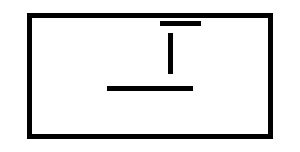
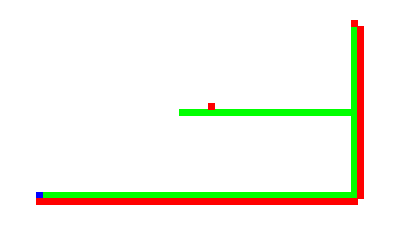
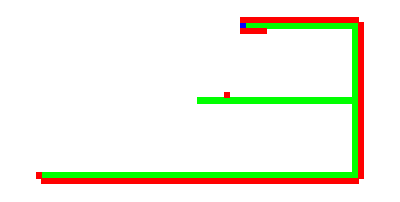
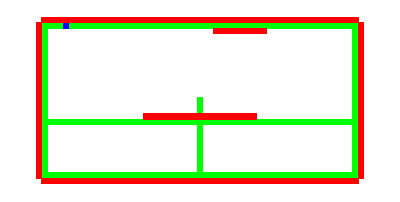
```mathematica
Grid[
{{"Simulation time","Map","Discovered surface"},
{"150 seconds",-Graphics-,-Graphics-},
{"300 seconds",-Graphics-,-Graphics-},
{"600 seconds",-Graphics-,-Graphics-}

},Frame->All
]
```

Simulation time | Map | Discovered surface
150 seconds | -Graphics- | -Graphics-
300 seconds | -Graphics- | -Graphics-
600 seconds | -Graphics- | -Graphics-

Map size of 40 × 40 blocks

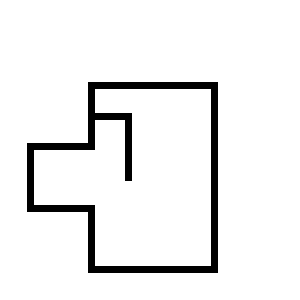
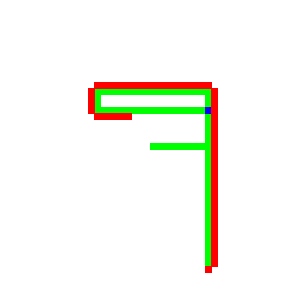
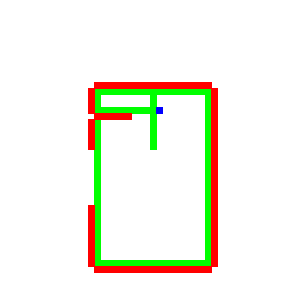
```mathematica
Grid[
{{"Simulation time","Map","Discovered surface"},
{"150 Seconds",-Graphics-,-Graphics-},
{"300 seconds",-Graphics-,-Graphics-}

},Frame->All
]
```

Simulation time | Map | Discovered surface
150 Seconds | -Graphics- | -Graphics-
300 seconds | -Graphics- | -Graphics-

Map size of 60 × 60 blocks

### Robot construction

## Main Results

## Wolfram|Alpha Linguistics

## Demonstrations

### Software simulation

```mathematica
updateSensorsSim[currentPosition_List, map_List]:=
Block[
{collisions,sensorState},

collisions={
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]+1}],
MemberQ[map,{currentPosition[[1]]+1,currentPosition[[2]]}],
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]-1}],
MemberQ[map,{currentPosition[[1]]-1,currentPosition[[2]]}]};

sensorState=Table[If[collisions[[i]]==True,1,0],{i,Length[collisions]}];
sensorState
]
```

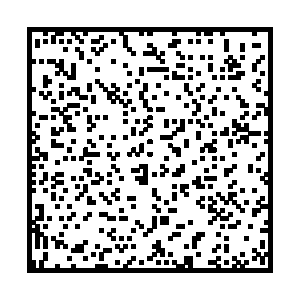

```mathematica
a4=Table[{-30,i},{i,-30,30}];
b4=Table[{30,i},{i,-30,30}];
c4=Table[{i,-30},{i,-30,30}];
d4=Table[{i,30},{i,-30,30}];
borders4=Join@@{a4,b4,c4,d4};
obstacles4=Table[{RandomInteger[{-30,30}],RandomInteger[{-30,30}]},{i,800}];
map4=DeleteCases[Join[borders4,obstacles4],{0,0}];
Graphics[Rectangle/@map4,ImageSize->300,PlotRange->{{-30,31},{-30,31}}]
```

```mathematica
position={0,0};
velocity={1,1}; 

discoveredMap={{0,0}};
walls={{}};
directions={"Forward","Right","Back","Left"};
sensors=updateSensorsSim[position,map4];
pause=1;

nextDirection=RandomChoice[directions];

status={TimeObject[Now],position,nextDirection,sensors,walls,discoveredMap};
test={};

Do[
timestampNew=TimeObject[Now];
previousStatus=status;
positionNew=updatePosition[timestampNew,previousStatus,velocity];
sensors=updateSensorsSim[positionNew,map4];

wallsNew=updateWalls2[positionNew,previousStatus,sensors];

mapNew=updateMap[positionNew,timestampNew,previousStatus];

nextDirection=updateDirection2[directions,sensors,previousStatus[[3]]];
status={timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew};
test=Append[test,status];
Pause[pause];
,{loop,100}]
```

```mathematica
Manipulate[
Overlay[
{
Graphics[{Green,Rectangle/@test[[frame,6]],Blue,Rectangle[test[[frame,2]]],Style[Rectangle/@DeleteCases[test[[frame,5]],{}],Red]},PlotRange->{{test[[frame,2,1]]-40,test[[frame,2,1]]+40},{test[[frame,2,2]]-40,test[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[test[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[test[[frame,6,i]],{-1}],{i,Length[test[[frame,6]]]}],

Style[Cuboid/@Table[If[test[[frame,5,i]]=={},Nothing,Join[DeleteCases[test[[frame,5,i]],{}],{0}]],{i,Length[test[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{test[[frame,2,1]]-5,test[[frame,2,1]]+5},{test[[frame,2,2]]-5,test[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[test],1}]
```

-Graphics-

## Conclusions

The project concluded with a working solution to the SLAM problem. Simulations have shown that the algorithm operates best in places with a high amount of obstacles, whilst tests with the robot indicate the need for a control system to accommodate variations in movement.

## Open Problems

Add support for other sensors

LiDAR systems

Raspberry Pi Camera

Kinect

Add PID control to robot movement

Implement Extended Kalman Filters to allow the robot a more accurate method to alter its direction based on measurements

## Links/References

[1] Søren Riisgaard and Morten Rufus Blas.  SLAM for Dummies. (Massachusetts Institute of Technology: MIT OpenCourseWare), http://ocw.mit.edu (Accessed 24 Jun, 2016). 
[2] Brian Williams. 16.412J Cognitive Robotics, Spring 2005. (Massachusetts Institute of Technology: MIT OpenCourseWare), http://ocw.mit.edu (Accessed 24 Jun, 2016). 
[3] National Instruments. Robotics Fundamentals Series. November 2014. (National Instruments), http://www.ni.com/white-paper/8187/en/ (Accessed 24 Jun, 2016)

## Keywords

Raspberry Pi

Robotics

Wolfram Science Summer School 2016

## Other

Last Modified: Thursday, July 07, 2016

"Insert date..."